# Physikbasierte Modellierung und Simulation

## Aufgabe 9.1

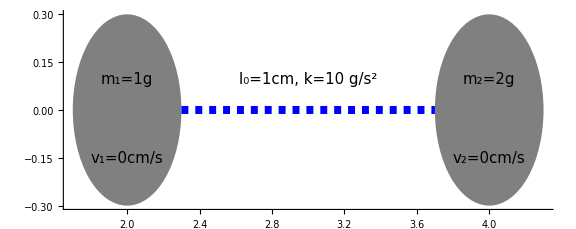

```mathematica
Graphics[{Gray,Disk[{2,0},0.3],Disk[{4,0},0.3], Black,Text[Style["m_1=1g", FontSize->15], {2,0.1}], Text[Style["m_2=2g",FontSize->15], {4,0.1}], Thickness[0.01], Blue, Dashed, Line[{{2.3,0},{3.7,0}}], Black, Text[Style["v_2=0cm/s", FontSize->15], {4,-0.15}],Text[Style["v_1=0cm/s", FontSize->15], {2,-0.15}],Text[Style["l_0=1cm, k=10 g/s^2", FontSize->15], {3,0.1}]}, Axes->{True, False}, AxesOrigin->{0,0}, ImageSize->Large]
```

## Aufgabe 9.2

Hooke’s Gesetz: F=k(l_0-l) mit Betrachtung der Richtung der Kraft:
⇒ F_1=k(l_0-|x_1-x_2|)*(x_1-x_2)/(|x_1-x_2|)=10 g/s^2(1cm-|2cm-4cm|)*(2cm-4cm)/(|2cm-4cm|)=10 g/s^2(-1cm)*(-1)=10cm g/s^2
⇒ F_2=k(l_0-|x_2-x_1|)*(x_2-x_1)/(|x_2-x_1|)=10 g/s^2(1cm-|4cm-2cm|)*(4cm-2cm)/(|4cm-2cm|)=10 g/s^2(-1cm)*1=-10cm g/s^2

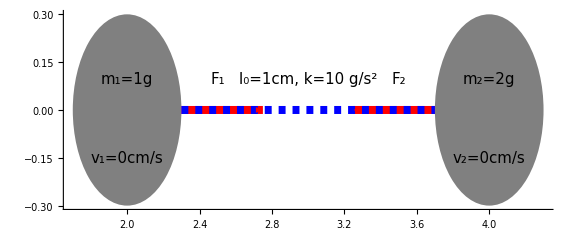

```mathematica
Graphics[{Gray,Disk[{2,0},0.3],Disk[{4,0},0.3], Black,Text[Style["m_1=1g", FontSize->15], {2,0.1}], Text[Style["m_2=2g",FontSize->15], {4,0.1}], Thickness[0.01], Black, Text[Style["v_2=0cm/s", FontSize->15], {4,-0.15}],Text[Style["v_1=0cm/s", FontSize->15], {2,-0.15}], Text[Style["l_0=1cm, k=10 g/s^2", FontSize->15], {3,0.1}], Text[Style["F_1", FontSize->15], {2.5,0.1}],Text[Style["F_2", FontSize->15], {3.5,0.1}],Red, Arrow[{{2.3,0},{2.75,0}}], Arrow[{{3.7,0},{3.25,0}}],Blue, Dashed, Line[{{2.3,0},{3.7,0}}]}, Axes->{True, False}, AxesOrigin->{0,0},ImageSize->Large]
```

## Aufgabe 9.3

x_1(t+h)=x_1(t)+h x_1'(t)=x_1(t)+h v_1(t)=2cm +1 s * 0 cm/s=2cm
x_2(t+h)=x_2(t)+h x_2'(t)=x_2(t)+h v_2(t)=4cm +1 s * 0 cm/s=4cm

a_1(t)=F_1/m_1=(10cm *g)/(s^2*1 g)=10 cm/s^2
a_2(t)=F_2/m_2=(-10cm *g)/(s^2*2 g)=-5 cm/s^2

v_1(t+h)=v_1(t)+h v_1'(t)=v_1(t)+h a_1(t)=0 cm/s+1s*10 cm/s^2=10 cm/s
v_2(t+h)=v_2(t)+h v_2'(t)=v_2(t)+h a_2(t)=0 cm/s+1s*-5 cm/s^2=-5 cm/s

Nicht stabil, da sich im nächsten Schritt beide Kugeln durchdringen werden; kausal nicht erklärbar.

## Aufgabe 9.4

a)
Da hier auf jeden Fall: x_2>x_1 gilt, können F_1 und F_2 wie folgt vereinfacht werden:
F_1(x_1, x_2)=k(l_0-(-(x_1-x_2)))*(x_1-x_2)/(-(x_1-x_2))=-k(l_0+x_1-x_2)
F_2(x_1, x_2)=k(l_0-(x_2-x_1))*(x_2-x_1)/(x_2-x_1)=k(l_0+x_1-x_2)

Damit ist die Jakobi-Matrix:
J=((∂F_1)/(∂x_1) | (∂F_1)/(∂x_2)
(∂F_2)/(∂x_1) | (∂F_2)/(∂x_2))=(-k | k
k | -k)

b)
(m_1 a_1'
m_2 a_2')=(F_1
F_2)+h J (v_1
v_2)+h^2 J (a_1'
a_2')=(10
-10)cm g/s^2+ 1 s * (-10 | 10
10 | -10) g/s^2*(0
0)cm/s+ (1s)^2*(-10 | 10
10 | -10) g/s^2(a_1'
a_2')
⧦
(1 | 0
0 | 2)(a_1'
a_2')g=(10
-10)cm g/s^2+(-10 | 10
10 | -10) (a_1'
a_2')g  | :g | - (-10 | 10
10 | -10) (a_1'
a_2')
⧦
(10
-10)cm/s^2=(11 | -10
-10 | 12)(a_1'
a_2')
⧦
(a_1'
a_2')=(3/8 | 5/16
5/16 | 11/32)(10
-10)cm/s^2
⧦
(a_1'
a_2')=(5/8
-5/16)cm/s^2

c)
(v_1'
v_2')=(v_1
v_2)+h(a_1'
a_2)=(0
0)cm/s+1s*(5/8
-5/16)cm/s^2=(5/8
-5/16)cm/s
(x_1'
x_2')=(x_1
x_2)+h(v_1'
v_2)=(2
4)cm+1s*(5/8
-5/16)cm/s=(21/8
59/16)cm=(2.625
3.6875)cm